Last modified on: Saturday, June 30, 2018 at 23:52

Author Info

James Pedersen

Vladimir Grankovsky

University of Washington

Poster Session Content

On the Road to a Gravitational Computer: Encoding Basic Programs in Terms of the Three-Body Program

To find methods by which basic programs, such as addition and multiplication, can be encoded in terms of the (Newtonian) three-body problem.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics-

I began work on a algorithm to transform a known spiral-like solution to the three-body problem into a form (like that in the above image) that encodes the multiplication of two numbers.

Find stable spiral-like solutions to the three-body problem where the three bodies eventually undergo a triple collision. 

Train a neural network to encode any computer program in terms of the three-body problem: 
-Graphics-

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

The Idea:

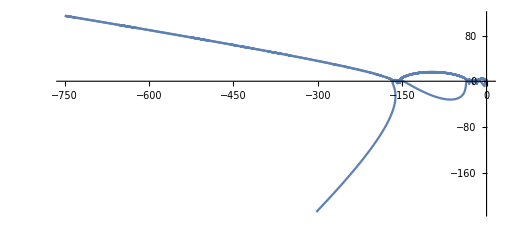
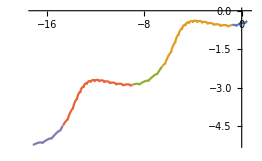
Start with a trajectory like so: 
-Graphics-

and then repeatedly perturb the initial conditions, at each iteration choosing the solution whose form is closest to the desired form.
-Graphics--Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

The initial goal of my project was to use machine learning to classify solutions to the three-body problem. However, I ran into problems with this. When trying to label three-bodies according to the classification scheme produced by Nicholas Lucas, a WSS student in 2013, frequently I would encounter a trajectory that could easily fall into two (or sometimes even three) of his classes. I subsequently changed the direction of the project and attempted to write an algorithm to encode multiplication in terms of the three-body problem. I began work on an algorithm that given two positive numbers x and y, attempts to find an initial condition to the three-body problem which produces a spirally trajectory that encodes x times y (see the image of the first page). 

I was trying to make progress on the hypothesis that the three-body problem is computationally universal (or Turing complete). This means that there exists an encoding function g (that converts initial conditions to three-body initial conditions) and a decoding function h (that converts a three-body initial condition to the output of a Turing machine) such that given any Turing machine x, h(g(x)) = x, or said another way, any computer program can be turned into an initial condition to the three-body problem which, after being simulated, can somehow be decoded into the output of the original computer program.

#### Code

https://github.com/watcher00090/Summer2018Starter/tree/master/Project

#### Future Directions

The neural network approach seems promising. To show computational universality of the three-body problem it is sufficient to produce encoder and decoder functions that never halt, and neural networks never halt [1]. Furthermore, “recurrent neural networks are Turing machines”, in a sense [2]. 

[1] https://education.wolfram.com/summer/school/resources/science-notes/ (enumeration and irreducibility)
[2]: http://lipas.uwasa.fi/stes/step96/step96/hyotyniemi1/